1 - 5 Similar matrices have equal eigenvalues
Verify this for A and A = P^-1A P. If y is an eigenvector of P, show that x = P y are eigenvectors of A.

1.  A=(3 | 4
4 | -3), P=(-4 | 2
3 | -1)

```mathematica
Clear["Global`*"]
```

```mathematica
AA=({{3, 4}, {4, -3}})
```

{{3,4},{4,-3}}

```mathematica
PP=({{-4, 2}, {3, -1}})
```

{{-4,2},{3,-1}}

```mathematica
e1=Inverse[PP]
```

{{1/2,1},{3/2,2}}

```mathematica
e2=e1.AA.PP
```

{{-25,12},{-50,25}}

```mathematica
e3={vals,vecs}=Eigensystem[e2]
```

{{-5,5},{{3,5},{2,5}}}

```mathematica
e4={vals,vecs}=Eigensystem[PP]
```

{{1/2 (-5-√33),1/2 (-5+√33)},{{1/6 (-3-√33),1},{1/6 (-3+√33),1}}}

```mathematica
e5={vals,vecs}=Eigensystem[AA]
```

{{-5,5},{{-1,2},{2,1}}}

Above: Some basic declarations and calculations to set up the problem. The spectrum matches the text answer, i.e. I have that the eigenvalues of the melange equal the eigenvalues of AA.

```mathematica
e14=e1.{-1,2}
```

{3/2,5/2}

```mathematica
e15=e2.{3/2,5/2}==-5{3/2,5/2}
```

True

```mathematica
e16=e1.{2,1}
```

{2,5}

```mathematica
e17=e2.{2,5}==5 {2,5}
```

True

Above. This confirms the second half of Theorem 3, sec 8.4, p. 340. I know the theorem states that eigenvectors of aA are good with the melange (after being dotted with Inverse[pP]), but not the other way round. The other way round is what this problem instruction is trying to establish. Is it enforceable?

```mathematica
e19=PP.{3,5}
```

{-2,4}

```mathematica
e20=AA.e19==-5 e19
```

True

```mathematica
e21=PP.{2,5}
```

{2,1}

```mathematica
e22=AA.e21==5 e21
```

True

Above: Okay, it works. That explains where those x vectors in the answer came from. The eigenvectors from the melange work when dotted with pP.

3.  A=(8 | -4
2 | 2), P=(0.28 | 0.96
-0.96 | 0.28)

```mathematica
Clear["Global`*"]
```

```mathematica
aA=({{8, -4}, {2, 2}})
```

{{8,-4},{2,2}}

```mathematica
pP=({{0.28, 0.96}, {-0.96, 0.28}})
```

{{0.28,0.96},{-0.96,0.28}}

```mathematica
e1=Inverse[pP]
```

{{0.28,-0.96},{0.96,0.28}}

```mathematica
e2=e1.aA.pP
```

{{3.008,-0.544},{5.456,6.992}}

```mathematica
e3={vals,vecs}=Eigensystem[aA]
```

{{6,4},{{2,1},{1,1}}}

```mathematica
e4={vals,vecs}=Eigensystem[e2]
```

{{6.,4.},{{0.178885,-0.98387},{-0.480833,0.876812}}}

Above: aA and the melange share eigenvalues.

```mathematica
e5={vals,vecs}=Eigensystem[pP]
```

{{0.28+0.96 ⅈ,0.28-0.96 ⅈ},{{0.707107+0. ⅈ,0.+0.707107 ⅈ},{0.707107+0. ⅈ,0.-0.707107 ⅈ}}}

```mathematica
e6=e1.{2,1}
```

{-0.4,2.2}

```mathematica
e7=e2.e6==6 e6
```

True

```mathematica
e8=e1.{1,1}
```

{-0.68,1.24}

```mathematica
e9=e2.e8==4 e8
```

True

Above, e6 through e9: eigenvectors of aA, after being dotted with Inverse[pP], work as eigenvectors of the melange.

```mathematica
e10=pP.{0.17888543819998307,-0.9838699100999075}
```

{-0.894427,-0.447214}

```mathematica
e11=aA.e10==6 e10
```

True

```mathematica
e12=pP.{-0.48083261120685233,0.8768124086713189}
```

{0.707107,0.707107}

```mathematica
e13=aA.e12==4 e12
```

True

Above, e10 through e13: eigenvectors of the melange, after being dotted with pP, work as eigenvectors of aA.

5.  A=(-5 | 0 | 15
3 | 4 | -9
-5 | 0 | 15), P=(0 | 1 | 0
1 | 0 | 0
0 | 0 | 1)

```mathematica
Clear["Global`*"]
```

```mathematica
aA=({{-5, 0, 15}, {3, 4, -9}, {-5, 0, 15}})
```

{{-5,0,15},{3,4,-9},{-5,0,15}}

```mathematica
pP=({{0, 1, 0}, {1, 0, 0}, {0, 0, 1}})
```

{{0,1,0},{1,0,0},{0,0,1}}

```mathematica
e1=Inverse[pP]
```

{{0,1,0},{1,0,0},{0,0,1}}

```mathematica
e2=e1.aA.pP
```

{{4,3,-9},{0,-5,15},{0,-5,15}}

```mathematica
e3={vals,vecs}=Eigensystem[aA]
```

{{10,4,0},{{1,-1,1},{0,1,0},{3,0,1}}}

```mathematica
e4={vals,vecs}=Eigensystem[pP]
```

{{-1,1,1},{{-1,1,0},{0,0,1},{1,1,0}}}

```mathematica
e5={vals,vecs}=Eigensystem[e2]
```

{{10,4,0},{{-1,1,1},{1,0,0},{0,3,1}}}

Above: it is seen that aA and the melange share the same eigenvalues, {10,4,0}.

```mathematica
e6=e1.{1,-1,1}
```

{-1,1,1}

```mathematica
e7=e2.e6==10 e6
```

True

```mathematica
e8=e1.{0,1,0}
```

{1,0,0}

```mathematica
e9=e2.e8==4 e8
```

True

```mathematica
e10=e1.{3,0,1}
```

{0,3,1}

```mathematica
e11=e2.e10==0 e10
```

True

Above, e6 through e11: it is seen that the eigenvectors of aA work as eigenvectors for the melange if first dotted with Inverse[pP].

```mathematica
e12=pP.{-1,1,1}
```

{1,-1,1}

```mathematica
e13=aA.e12==10 e12
```

True

```mathematica
e14=pP.{1,0,0}
```

{0,1,0}

```mathematica
e15=aA.e14==4 e14
```

True

```mathematica
e16=pP.{0,3,1}
```

{3,0,1}

```mathematica
e17=aA.e16==0 e16
```

True

Above, e12 through e17: it is seen that the eigenvectors of the melange work as eigenvectors for aA if first dotted with pP.

9 - 16 Diagonalization of matrices
Find an eigenbasis (a basis of eigenvectors) and diagonalize.

9.  (1 | 2
2 | 4)

Example 4 on p. 342 shows how to get this done.

```mathematica
Clear["Global`*"]
```

```mathematica
aA=({{1, 2}, {2, 4}})
```

{{1,2},{2,4}}

Find the eigenvectors

```mathematica
e1={vals,vecs}=Eigensystem[aA]
```

{{5,0},{{1,2},{-2,1}}}

Make a matrix of a couple of the eigenvectors, think of this as P from above

```mathematica
e2=({{1, -2}, {2, 1}})
```

{{1,-2},{2,1}}

Get the inverse of the eigenvector matrix, this will be Pᵀ

```mathematica
e4=Inverse[e2]
```

{{1/5,2/5},{-2/5,1/5}}

Then muliply to make a conglomerate.

```mathematica
e4.aA.e2
```

{{5,0},{0,0}}

Above: This is what I need. It is already diagonalized. The answer agrees with the text.

11.  (-19 | 7
-42 | 16)

```mathematica
Clear["Global`*"]
```

```mathematica
e1=({{-19, 7}, {-42, 16}})
```

{{-19,7},{-42,16}}

```mathematica
e2={vals,vecs}=Eigensystem[e1]
```

{{-5,2},{{1,2},{1,3}}}

```mathematica
e3=({{1, 1}, {2, 3}})
```

{{1,1},{2,3}}

```mathematica
e4=Inverse[e3]
```

{{3,-1},{-2,1}}

```mathematica
e5=e4.e1.e3
```

{{-5,0},{0,2}}

```mathematica
Det[e5]
```

-10

```mathematica
e6={{2,0},{0,-5}}
```

{{2,0},{0,-5}}

```mathematica
Det[e6]
```

-10

```mathematica
Eigenvalues[e5]
```

{-5,2}

```mathematica
Eigenvalues[e6]
```

{-5,2}

Above: Mathematica has found e5 as the answer, but the text shows e6. e5 and e6 have the same determinant, trace, and eigenvalues, and I suspect they are similar. However, I do not know how to find P such that e6=P^-1.e5.P, so I can’t take a green.

13.  (4 | 0 | 0
12 | -2 | 0
21 | -6 | 1)

```mathematica
Clear["Global`*"]
```

```mathematica
e1=({{4, 0, 0}, {12, -2, 0}, {21, -6, 1}})
```

{{4,0,0},{12,-2,0},{21,-6,1}}

```mathematica
e2={vals,vecs}=Eigensystem[e1]
```

{{4,-2,1},{{1,2,3},{0,1,2},{0,0,1}}}

```mathematica
e3=({{1, 0, 0}, {2, 1, 0}, {3, 2, 1}})
```

{{1,0,0},{2,1,0},{3,2,1}}

```mathematica
e4=Inverse[e3]
```

{{1,0,0},{-2,1,0},{1,-2,1}}

```mathematica
e5=e4.e1.e3
```

{{4,0,0},{0,-2,0},{0,0,1}}

Above: The looked-for diagonalized matrix. The text answer agrees.

15. (4 | 3 | 3
3 | 6 | 1
3 | 1 | 6)

```mathematica
Clear["Global`*"]
```

```mathematica
e1=({{4, 3, 3}, {3, 6, 1}, {3, 1, 6}})
```

{{4,3,3},{3,6,1},{3,1,6}}

```mathematica
e2={vals,vecs}=Eigensystem[e1]
```

{{10,5,1},{{1,1,1},{0,-1,1},{-2,1,1}}}

```mathematica
e3=({{1, 0, -2}, {1, -1, 1}, {1, 1, 1}})
```

{{1,0,-2},{1,-1,1},{1,1,1}}

```mathematica
e4=Inverse[e3]
```

{{1/3,1/3,1/3},{0,-1/2,1/2},{-1/3,1/6,1/6}}

```mathematica
e5=e4.e1.e3
```

{{10,0,0},{0,5,0},{0,0,1}}

Above: another similar-looking lookalike. The text gives the answer {{10,0,0},{0,1,0},{0,0,5}}.

```mathematica
e6={{10,0,0},{0,1,0},{0,0,5}}
```

{{10,0,0},{0,1,0},{0,0,5}}

```mathematica
Det[e5]
```

50

```mathematica
Det[e6]
```

50

```mathematica
Eigenvalues[e5]
```

{10,5,1}

```mathematica
Eigenvalues[e6]
```

{10,5,1}

```mathematica
Tr[e5]
```

16

```mathematica
Tr[e6]
```

16

Again, I can’t prove they are similar, but it’s suggestive.

17 - 23 Principal axes. Conic sections
What kind of conic section (or pair of straight lines) is given by the quadratic form? Transform it to principal axes. Express xᵀ = {x_1, x_2} in terms of the new coordinate vector yᵀ = {y_1, y_2} , as in example 6, p. 344.

17.  7 x_1^2+6 x_1 x_2+7 x_2^2=200

```mathematica
Clear["Global`*"]
```

```mathematica
e1=7 x1^2+6 x1 x2+7 x2^2==200
```

7 x1^2+6 x1 x2+7 x2^2==200

```mathematica
e2=({{7, 3}, {3, 7}})
```

{{7,3},{3,7}}

Above: The text answer identifies the matrix as C.

```mathematica
e3={x1, x2}
```

{x1,x2}

```mathematica
e4=e3.e2.e3
```

x1 (7 x1+3 x2)+x2 (3 x1+7 x2)

```mathematica
e5=Expand[e4]
```

7 x1^2+6 x1 x2+7 x2^2

```mathematica
e6={vals,vecs}=Eigensystem[e2]
```

{{10,4},{{1,1},{-1,1}}}

Above: according to example 6, p. 344, numbered line (10) on p 343 becomes:

```mathematica
e7=10 y1^2+4 y2^2
```

10 y1^2+4 y2^2

And further,

```mathematica
e8=e7==200
```

10 y1^2+4 y2^2==200

Above: the equation is the same as in the text, except numbering of constants is reversed.

```mathematica
e9=e8/.{(10 y1^2+4 y2^2)->((10 y1^2)/200+(4 y2^2)/200),200->1}
```

y1^2/20+y2^2/50==1

Above: this is the line where the type of conic section is identified. Here there are different coefficients to the squared terms, and the signs are the same. This identifies an ellipse.

```mathematica
e10=e2-10 IdentityMatrix[2]
```

{{-3,3},{3,-3}}

Above: the part of example 6, p. 344 where normalized eigenvectors are calculated.

```mathematica
e11=Thread[e10.e3==0]
```

{-3 x1+3 x2==0,3 x1-3 x2==0}

```mathematica
e12=Solve[e11]
```

{{x2→x1}}

```mathematica
e16={1,1}
```

{1,1}

Above: the components of the first eigenvector have been calculated.

```mathematica
e13=e2-4 IdentityMatrix[2]
```

{{3,3},{3,3}}

```mathematica
e14=Thread[e13.e3==0]
```

{3 x1+3 x2==0,3 x1+3 x2==0}

```mathematica
e15=Solve[e14]
```

{{x2→-x1}}

Above: This looks good. However, the vectors are supposed to be orthonormal.  They need to be normalized.

```mathematica
e16n=Normalize[e16]
```

{1/(√2),1/(√2)}

```mathematica
e17={1,-1}
```

{1,-1}

```mathematica
e17n=Normalize[e17]
```

{1/(√2),-1/(√2)}

```mathematica
e18=({{1/(√2), 1/(√2)}, {1/(√2), -1/(√2)}})
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

Above: the matrix of eigenvectors is put together by hand.

```mathematica
e19={y1,y2}
```

{y1,y2}

```mathematica
e20=Thread[e18.e19==e3]
```

{y1/(√2)+y2/(√2)==x1,y1/(√2)-y2/(√2)==x2}

This mostly matches the text. Perhaps the rotation would be opposite to the text. In Wikipedia is an article on the Principal axis theorem, which was of use.

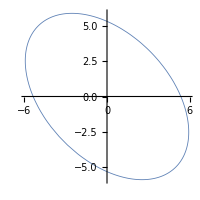

```mathematica
ParametricPlot[{√20 Cos[t] Cos[π/4]-√50 Sin[t] Sin[π/4],√20 Cos[t] Sin[π/4]+√50 Sin[t] Cos[π/4]},{t,0,2 π},ImageSize->200,PlotStyle->Thickness[0.003]]
```

Above: Would this be it, or would it go the other way? If I had to label x1 and x2 axes, which would be which?

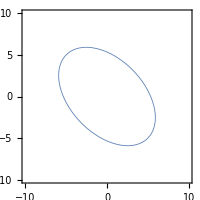

```mathematica
ContourPlot[7 x1^2+6 x1 x2+7 x2^2==200,{x1,-10,10},{x2,-10,10},ImageSize->200,ContourStyle->Thickness[0.003]]
```

Above: Bravo home team.

19.  3 x_1^2+22 x_1 x_2+3 x_2^2=0

```mathematica
Clear["Global`*"]
```

```mathematica
e1=({{3, 11}, {11, 3}})
```

{{3,11},{11,3}}

Above: The matrix identified in the text answer.

```mathematica
e2={x1,x2}
```

{x1,x2}

```mathematica
e3=e2.e1.e2
```

x2 (11 x1+3 x2)+x1 (3 x1+11 x2)

```mathematica
e4=Expand[e3]
```

3 x1^2+22 x1 x2+3 x2^2

```mathematica
e5={vals,vecs}=Eigensystem[e1]
```

{{14,-8},{{1,1},{-1,1}}}

Below: According to example6, p. 344, expression (10) on p 343 becomes

```mathematica
e6=14 y1^2-8 y2^2
```

14 y1^2-8 y2^2

Below: and further,

```mathematica
e7=14 y1^2-8 y2^2==0
```

14 y1^2-8 y2^2==0

Above: this is the line where the type of conic section is identified. The signs on the squared terms are opposite, which would normally indicate a hyperbola. However, the equation is equal to zero, and I guess that’s what makes it a pair of lines. The equation appears in the text answer.

```mathematica
e8=e1-14 IdentityMatrix[2]
```

{{-11,11},{11,-11}}

Above: the part of example 6, p. 344 where normalized eigenvectors are calculated.

```mathematica
e9=Thread[e8.e2==0]
```

{-11 x1+11 x2==0,11 x1-11 x2==0}

```mathematica
e10=Solve[e9]
```

{{x2→x1}}

```mathematica
e11={1,1}
```

{1,1}

```mathematica
e12=Normalize[e11]
```

{1/(√2),1/(√2)}

Above: one normalized vector down, one to go.

```mathematica
e13=e1+8 IdentityMatrix[2]
```

{{11,11},{11,11}}

```mathematica
e14=Thread[e13.e2==0]
```

{11 x1+11 x2==0,11 x1+11 x2==0}

```mathematica
e15=Solve[e14]
```

{{x2→-x1}}

```mathematica
e16={1,-1}
```

{1,-1}

```mathematica
e17=Normalize[e16]
```

{1/(√2),-1/(√2)}

Above: both normalized eigenvectors have been found.

```mathematica
e18=({{1/(√2), 1/(√2)}, {1/(√2), -1/(√2)}})
```

{{1/(√2),1/(√2)},{1/(√2),-1/(√2)}}

Above: the matrix of eigenvectors is put together by hand. The expression appears in the text.

```mathematica
e19={y1,y2}
```

{y1,y2}

```mathematica
e20=Thread[e18.e19==e2]
```

{y1/(√2)+y2/(√2)==x1,y1/(√2)-y2/(√2)==x2}

Above: it looks like something has a 45 degree rotation. But it is not an ellipse. This time the answers match the text well. The text says pair of straight lines, which is obvious, since all factors are linear.

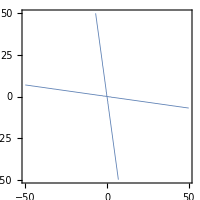

```mathematica
ContourPlot[3 x1^2+22 x1 x2+3 x2^2==0,{x1,-50,50},{x2,-50,50},ImageSize->200,ContourStyle->Thickness[0.003]]
```

Above: with new tool, ContourPlot, the plot is easily executed.

21.  x_1^2-12 x_1 x_2+x_2^2=70

```mathematica
Clear["Global`*"]
```

I am at example 6, p. 344. The coefficients for the squared terms are equal here as in example 6, and they make up the diagonal. The x_1 x_2 term is divided in half and makes up the off-diagonal ‘corners’ of the matrix.

```mathematica
e1=({{1, -6}, {-6, 1}})
```

{{1,-6},{-6,1}}

Above: The matrix C is identified as per the text.

```mathematica
e2={x1,x2}
```

{x1,x2}

Below: The polynomial equation’s coefficients are made from the above matrix, the 1 and the 6.

```mathematica
Solve[(1-λ)^2-(6)^2==0,λ]
```

{{λ→-5},{λ→7}}

And the polynomial is readily available as

```mathematica
e7=7 Subscript[y, 1]^2-5 Subscript[y, 2]^2==70
```

7 y_1^2-5 y_2^2==70

Above: this is the line where the type of conic section is identified. The squared factors differ in sign, and the sum is greater than zero. Hence it is a hyperbola. It agrees with text.

Below: beginning the part of example6, p. 344 where normalized eigenvectors are calculated based on
(A-λ I)x=0, and for this case λ_1 = 7 and λ_2 = -5.

So,

```mathematica
e8=e1-7 IdentityMatrix[2]
```

{{-6,-6},{-6,-6}}

```mathematica
e9=Thread[e8.e2==0]
```

{-6 x1-6 x2==0,-6 x1-6 x2==0}

```mathematica
e10=Solve[e9]
```

{{x2→-x1}}

```mathematica
e11={1,-1}
```

{1,-1}

```mathematica
e12=Normalize[e11]
```

{1/(√2),-1/(√2)}

Above: one normalized eigenvector down, one to go.

```mathematica
e13=e1+5 IdentityMatrix[2]
```

{{6,-6},{-6,6}}

```mathematica
e14=Thread[e13.e2==0]
```

{6 x1-6 x2==0,-6 x1+6 x2==0}

```mathematica
e15=Solve[e14]
```

{{x2→x1}}

```mathematica
e16={1,1}
```

{1,1}

```mathematica
e17=Normalize[e16]
```

{1/(√2),1/(√2)}

Above: both normalized eigenvectors have been found.

```mathematica
e18=({{1/(√2), 1/(√2)}, {-1/(√2), 1/(√2)}})
```

{{1/(√2),1/(√2)},{-1/(√2),1/(√2)}}

Above: the matrix of eigenvectors is put together by hand.

```mathematica
e19={y1,y2}
```

{y1,y2}

Following the wind-up section of example 6, and fetching the appropriate vectors connoting x_1, x_2, y_1, y_2 ,

```mathematica
e20=Thread[e18.e19==e2]
```

{y1/(√2)+y2/(√2)==x1,-y1/(√2)+y2/(√2)==x2}

The parametric version of the hyperbola in e7 would be x=2/(√70)secant t, y=(√5)/(√70)tangent t.

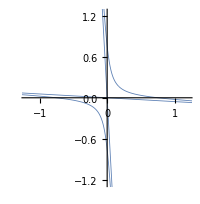

```mathematica
ParametricPlot[{2/(√70)Sec[t]Cos[π/4]-(√5)/(√70)Tan[t]Sin[π/4],2/(√70)Sec[t]Sin[π/4]+(√5)/(√70)Tan[t]Cos[π/4]},{t,0,2 π},ImageSize->200,PlotStyle->Thickness[0.003]]
```

Above: the plot shows the sign differences for multiple angle formula, I think. But does not take into account the sign differences for the problem equation. Those are tried out below:

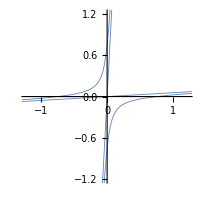

```mathematica
ParametricPlot[{2/(√70)Sec[t]Cos[-π/4]-(√5)/(√70)Tan[t]Sin[-π/4],2/(√70)Sec[t]Sin[-π/4]+(√5)/(√70)Tan[t]Cos[-π/4]},{t,0,2 π},ImageSize->200,PlotStyle->Thickness[0.003]]
```

Above: playing with the signs makes it come out looking more like it should.

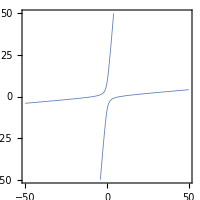

```mathematica
ContourPlot[x1^2-12 x1 x2+x2^2==70,{x1,-50,50},{x2,-50,50},ImageSize->200,ContourStyle->Thickness[0.003]]
```

23.  -11 x_1^2+84 x_1 x_2+24 x_2^2=156

```mathematica
Clear["Global`*"]
```

```mathematica
e1=({{-11, 42}, {42, 24}})
```

{{-11,42},{42,24}}

Above: the matrix C is identified and agrees with the text. Here I see the important difference made when the coefficients of the two squared terms are not equal. They both occupy the diagonal in their own identity.

```mathematica
e2={x1,x2}
```

{x1,x2}

From this point down to the next green cell, the ground covered is not exactly by shortcut by way of example 6, as it was in the procedure in problem 21.

```mathematica
e3=e2.e1.e2
```

x2 (42 x1+24 x2)+x1 (-11 x1+42 x2)

```mathematica
e4=Expand[e3]
```

-11 x1^2+84 x1 x2+24 x2^2

```mathematica
e5={vals,vecs}=Eigensystem[e1]
```

{{52,-39},{{2,3},{-3,2}}}

Below: According to example 6 on p. 344, expression (10), p. 343 becomes

```mathematica
e6=52 y1^2-39 y2^2
```

52 y1^2-39 y2^2

Below: and further,

```mathematica
e7=e6==156
```

52 y1^2-39 y2^2==156

Above: this is the line where the type of conic section is identified. The squared factors differ in sign, making it a hyperbola. It matches the equation in the text answer.

```mathematica
e8=e1-52 IdentityMatrix[2]
```

{{-63,42},{42,-28}}

```mathematica
e9=Thread[e8.e2==0]
```

{-63 x1+42 x2==0,42 x1-28 x2==0}

```mathematica
e10=Solve[e9]
```

{{x2→(3 x1)/2}}

```mathematica
e11={1,3/2}
```

{1,3/2}

```mathematica
e12=Normalize[e11]
```

{2/(√13),3/(√13)}

Above: one normalized eigenvector down, one to go.

```mathematica
e13=e1+39 IdentityMatrix[2]
```

{{28,42},{42,63}}

```mathematica
e14=Thread[e13.e2==0]
```

{28 x1+42 x2==0,42 x1+63 x2==0}

```mathematica
e15=Solve[e14]
```

{{x2→-(2 x1)/3}}

```mathematica
e16={1,-2/3}
```

{1,-2/3}

```mathematica
e17=Normalize[e16]
```

{3/(√13),-2/(√13)}

Above: both normalized eigenvectors have been found.

```mathematica
e18=({{2/(√13), 3/(√13)}, {3/(√13), -2/(√13)}})
```

{{2/(√13),3/(√13)},{3/(√13),-2/(√13)}}

Above: the matrix of eigenvectors is put together by hand. It matches the matrix shown in the text answer.

```mathematica
e19={y1,y2}
```

{y1,y2}

```mathematica
e20=Thread[e18.e19==e2]
```

{(2 y1)/(√13)+(3 y2)/(√13)==x1,(3 y1)/(√13)-(2 y2)/(√13)==x2}

The parametric version of the hyperbola in e7 would be x=√(52/156)secant t, y=√(39/156) tangent t.

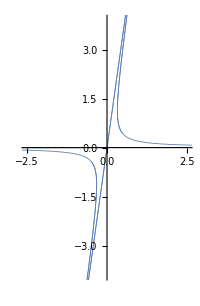

```mathematica
ParametricPlot[{√(52/156)Sec[t]Cos[2/(√13)]-√(39/156)Tan[t]Sin[3/(√13)],√(52/156)Sec[t]Sin[3/(√13)]+√(39/156)Tan[t]Cos[-2/(√13)]},{t,0,3 π},ImageSize->200,PlotStyle->Thickness[0.003]]
```

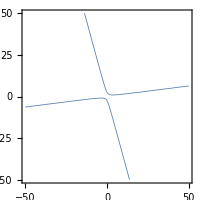

```mathematica
ContourPlot[-11 x1^2+84 x1 x2+24 x2^2==156,{x1,-50,50},{x2,-50,50},ImageSize->200,ContourStyle->Thickness[0.003]]
```

Above: evidently there is quite a way to go to understanding the principal axis theorem correctly.